```mathematica
Solve[S1*d==-(-σ-S1)*(d-t),S1]
```

{{S1→((d-t) σ)/t}}

```mathematica
S2=-σ-((d-t) σ)/t//FullSimplify
```

-(d σ)/t

```mathematica
-((d-t) σ)/t/.{d->t/2}
```

σ/2

```mathematica
(2*d-t)/t/.{d->t/2}
```

0

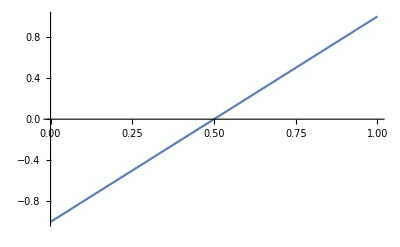

```mathematica
Plot[2*d-1,{d,0,1}]
```

```mathematica
ϕ[x_,y_,z_]:=1/Sqrt[x^2+(y-1)^2+z^2]-1/Sqrt[1/Sqrt[x^2+(y+1)^2+z^2]]
```

```mathematica
ϕ[0,0,0]
```

0

```mathematica
Sum[1/Sqrt[ρ^2+(z-(2*L*j+d)^2)]-1/Sqrt[ρ^2+(z-(2*L*j-d)^2)],{j,-100,100}]//FullSimplify
```

0

```mathematica
ϕ[ρ_,z_]:=1/Sqrt[ρ^2+(z-(2*L*j+d)^2)]-1/Sqrt[ρ^2+(z-(2*L*j-d)^2)]
```

```mathematica
D[ϕ[ρ,z],ρ]/.{z->0}
```

ρ/((-(-d+2 j L)^2+ρ^2)^(3/2))-ρ/((-(d+2 j L)^2+ρ^2)^(3/2))

```mathematica
D[ϕ[ρ,z],ρ]/.{z->L}
```

ρ/((L-(-d+2 j L)^2+ρ^2)^(3/2))-ρ/((L-(d+2 j L)^2+ρ^2)^(3/2))